```mathematica
(* taken from wolfram demos for binomial confidence intervals: http://demonstrations.wolfram.com/ConfidenceIntervalsForTheBinomialDistribution *)
```

```mathematica
(* j is successes, n is trials (attempts, samples ), p is probably the confidence? *) 
b[j_,n_,p_]:=CDF[BinomialDistribution[n,p],j];
intervals[jj_,nn_,confLvl_, opts___]:=Module[{t025=Quantile[NormalDistribution[],1 - (1-confLvl)/2],
blueSquare=Graphics[{Blue,Rectangle[]},ImageSize->10],redSquare=Graphics[{Red,Rectangle[]},ImageSize->10],blackSquare=Graphics[{Black,Rectangle[]},ImageSize->10],izq,der,interWald,interWilson,nums,int1,int2,int3,std,corrnums,stimes},
izq=Quiet@If[jj==1,0,(p/.NSolve[1-b[jj-1,nn,p]==(1-confLvl)/2,p])[[1]]];der=Quiet@(p/.NSolve[b[jj,nn,p]==(1-confLvl)/2,p])[[1]];
interWald=Max[0,#]&/@{jj/nn -t025  √(jj/nn (1-jj/nn)/nn),jj/nn +t025  √(jj/nn (1-jj/nn)/nn)};
interWilson={1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2-t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2))),1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2+t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2)))};int1=interWald;
int2=interWilson;
int3={izq,der};nums={interWald,interWilson,{izq,der}};
std=StringDrop[#,1]&/@(ToString/@(PaddedForm[#,{3,3}]&/@Flatten[nums]));difs=#[[2]]-#[[1]]&/@nums;
az=StringDrop[#,1]&/@(ToString/@(PaddedForm[#,{3,3}]&/@difs));
corrnums=Table["["<>std[[j]]<>","<>" "<>std[[j+1]]<>"]",{j,1,Length[std]-1,2}];stimes=Text[#]&/@Table[corrnums[[j]]<>"      "<>az[[j]],{j,1,3}];
ListLinePlot[{{jj/nn,0},{jj/nn,0.003}},Axes->{True,False},AxesOrigin->{0.25,0},PlotStyle->{Black,Thickness[0.001]},PlotRange->{{0,1},{-0.002,0.009}},Epilog->{Text[Style["j/n",Italic,Medium],{jj/nn,-0.00075}],Inset[Grid[{{Style[StringJoin[ToString[confLvl*100],"% confidence intervals"],Medium]},{Style["for the probability parameter",Medium]},{Style["in a binomial distribution",Medium]}}],{0.5,0.008}],Inset[Grid[{{Text["method"],Text[""],Text["  interval           length"]},{Text["conventional"],blueSquare,stimes[[1]]},{Text["Wilson"],redSquare,stimes[[2]]},{Text["Clopper-Pearson"],blackSquare,stimes[[3]]}}],{0.5,0.005}],Thick,Blue,Line@MapThread[List,{int1,{0.003,0.003}}],Thick,Red,Line@MapThread[List,{int2,{0.002,0.002}}],Thick,Black,Line@MapThread[List,{int3,{0.001,0.001}}]},opts]]
```

```mathematica
Manipulate[
If[successes>tries-2,successes=tries-2];
intervals[successes,tries,confidence, ImageSize->550],
{{successes,10},1,tries-2,1,Appearance->"Labeled"},
{{tries,50},20,200,5,Appearance->"Labeled"},{{confidence,0.95},0.5,0.99,0.01,Appearance->"Labeled"},SaveDefinitions->True]
```

```mathematica
(* redefining Wilson CI for convenience *) 
interWilson[jj_, nn_,confLvl_]:=Module[{t025=Quantile[NormalDistribution[],1 - (1-confLvl)/2]}, Interval[{1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2-t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2))),1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2+t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2)))}]]
```

```mathematica
(*** FILE MANIPULATIONS ***)
```

```mathematica
(* useful def*)
dataDirPath = "~/Dropbox/upenn/research/aa/monitoring_data/data/Session_4_Sonar_Nocontroller_8Aug2019/";
```

```mathematica
monFilenames[winSize_, idpairlist_] := StringJoin[dataDirPath, "Iteration_", ToString[#[[1]]], "/mon", ToString[#[[2]]], "_",ToString[winSize], "/iter", ToString[#[[1]]], "_mondet", ToString[#[[2]]], "_",ToString@winSize, "_estrates.txt"] & /@idpairlist;
```

```mathematica
(* useful def*)
allMonFilenames[winSize_] := StringJoin[dataDirPath, "Iteration_", ToString[#[[1]]], "/mon", ToString[#[[2]]], "_",ToString[winSize], "/iter", ToString[#[[1]]], "_mondet", ToString[#[[2]]], "_",ToString@winSize, "_estrates.txt"] & /@Flatten[Outer[List, Range[1,5], Range[1,5]], 1];
```

```mathematica
detFilenames[idpairlist_] := StringJoin[dataDirPath, "Iteration_", ToString[#[[1]]], "/det", ToString[#[[2]]], "/iter", ToString[#[[1]]], "_both_det_estrates.txt"] & /@idpairlist;
```

```mathematica
(* useful def*)
allDetFilenames = StringJoin[dataDirPath, "Iteration_", ToString[#[[1]]], "/det", ToString[#[[2]]], "/iter", ToString[#[[1]]], "_both_det_estrates.txt"] & /@Flatten[Outer[List, Range[1,5], Range[1,5]], 1];
```

```mathematica
(* add up a given field's values over filenames *) 
countFromFiles[fieldName_, filenames_] := Plus@@(*list of frame numbers from each*)(getValueFromListOfPairs[#,fieldName]& /@ (*list of all stat dicts*) (nameValuePairsFromFile/@filenames(*list of filenames*)))
```

```mathematica
(* H1 count from mons *) 
monH1ct = countFromFiles[ "h1count",allMonFilenames[10]]
```

580

```mathematica
(* FN count from mons *) 
monFNct = countFromFiles[ "FNcount",allMonFilenames[10]]
```

389

```mathematica
(* H0 count from dets *) 
detH0ct =countFromFiles[ "h0count",allDetFilenames]
```

1000

```mathematica
(* FP count from dets *) 
detFPct =countFromFiles[ "FPcount",allDetFilenames]
```

110

```mathematica
(* PREDICTIONS *) 
predFNR[detFPR_, monWin_, pDetNCH0_:0(* for here *)] := 1 - (1-detFPR)(1 - detFPR - pDetNCH0)^(monWin-1);
```

```mathematica
(* COMPARISON one shot *)
```

```mathematica
IntervalMemberQ[(* interval *) interWilson[countFromFiles[ "FNcount",allMonFilenames[10]], countFromFiles[ "h1count",allMonFilenames[10]], 0.95], (* prediction *) predFNR[countFromFiles[ "FPcount",allDetFilenames]/countFromFiles[ "h0count",allDetFilenames], 10]]
```

True

```mathematica
someSubsetList = {{1,1},{1,2},{1,3},{1,4},{1,5},{2,1},{2,2},{2,3}};
```

```mathematica
oneIntervalTest[pairIdList_] := IntervalMemberQ[(* interval *) interWilson[countFromFiles[ "FNcount",monFilenames[10, pairIdList]], countFromFiles[ "h1count",monFilenames[10, pairIdList]], 0.95], (* prediction *) predFNR[countFromFiles[ "FPcount",detFilenames[pairIdList]]/countFromFiles[ "h0count",detFilenames[pairIdList]], 10]];
```

```mathematica
oneIntervalTestPair[pairIdList_] := {(* interval *) interWilson[countFromFiles[ "FNcount",monFilenames[10, pairIdList]], countFromFiles[ "h1count",monFilenames[10, pairIdList]], 0.95], (* prediction *) predFNR[countFromFiles[ "FPcount",detFilenames[pairIdList]]/countFromFiles[ "h0count",detFilenames[pairIdList]], 10]};
```

```mathematica
(* testing over subsets of 23+ -- very favorable, around 1%. *) 
Tally[oneIntervalTest[#]&/@ Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {23, 25}]]
{{True,323},{False,3}}
```

{{True,323},{False,3}}

```mathematica
Length@Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1]] - 1
```

```mathematica
subsetCt = 33554431;
```

```mathematica
subsetCt23to25 = Length@Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {23,25}];
```

```mathematica
subsetCt20to25 = Length@Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {20,25}];
```

```mathematica
(* wow terrible stuff on small data, 15-20% error out of 100: *) 
Tally[oneIntervalTest[#]&/@ Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {1,25},{#}] &/@ RandomInteger[{1,subsetCt},100]]
```

{{{True},83},{{False},17}}

```mathematica
(* but good on big data, 0-2% error out of 100, weird: *)
```

```mathematica
Tally[oneIntervalTest[#]&/@ Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {23,25},{#}] &/@ RandomInteger[{1,subsetCt23to25},100]]
```

{{{True},100}}

```mathematica
(* medium data? 5-15% error out of 100 *)
```

```mathematica
Tally[oneIntervalTest[#]&/@ Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {20,25},{#}] &/@ RandomInteger[{1,subsetCt20to25},100]]
```

{{{True},92},{{False},8}}

```mathematica
(*** VISUALS FOR INTERVALS ***)
```

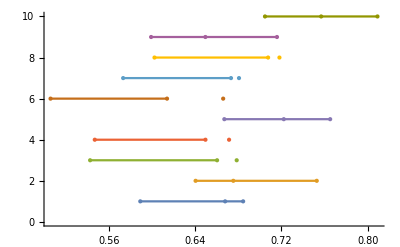

```mathematica
(* just a few samples *)
(* across all possible data -- poor performance *)
NumberLinePlot[oneIntervalTestPair[#]&/@ Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {1,25},{#}] &/@ RandomInteger[{1,subsetCt},10], PlotStyle->PointSize[Large]]
```

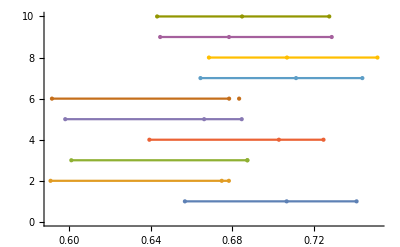

```mathematica
NumberLinePlot[oneIntervalTestPair[#]&/@ Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {20,25},{#}] &/@ RandomInteger[{1,subsetCt20to25},10], PlotStyle->PointSize[Large]]
```

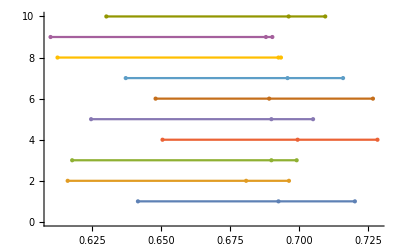

```mathematica
(* when substantial data is given -- good performance *)
NumberLinePlot[oneIntervalTestPair[#]&/@ Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {23,25},{#}] &/@ RandomInteger[{1,subsetCt23to25},10], PlotStyle->PointSize[Large]]
```

```mathematica
(* is the above right? why are confidence intervals not shrinking substantially?? in larger data *)
```

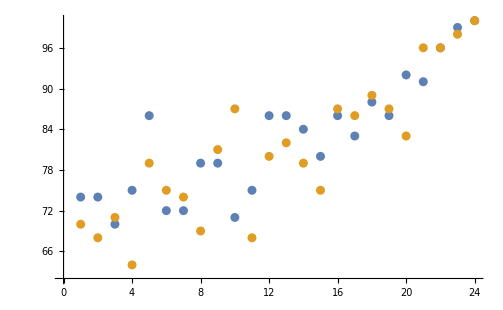
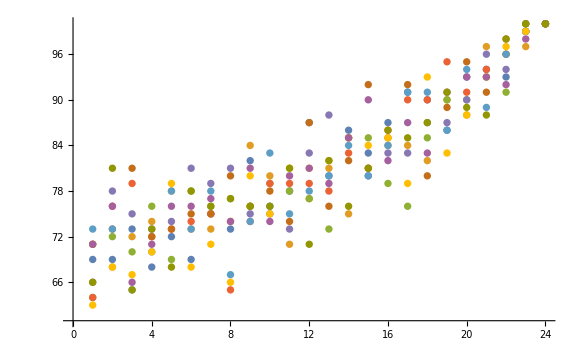
```mathematica
(* big samples *) 
(* get 100 random samples for every size of the subset, return the number of times the estimate is in the interval *)
generateSuccessCountsPerSubsetSize := With[{subsetsCt = #},
(* count truths *)Count[oneIntervalTest[#]&/@ (* all possible sets of pairs for tests *) Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt},{#}] &/@ (* getting random 100 subsets *)  RandomInteger[{1,(*counting subsets *)Length@Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt}]
},100], {True}]
]& /@ Range[1, 24];
reslist2= {70,68,71,64,79,75,74,69,81,87,68,80,82,79,75,87,86,89,87,83,96,96,98,100};
reslist1= {74,74,70,75,86,72,72,79,79,71,75,86,86,84,80,86,83,88,86,92,91,96,99,100};
(* get 10 lists of 100 samples like above *) 
reslists10 = Table[generateSuccessCountsPerSubsetSize, 10]
reslists10= {{69,69,73,68,72,69,75,73,82,76,78,87,80,86,83,87,91,90,86,93,94,93,100,100},{71,68,72,74,78,73,73,74,84,80,71,77,81,75,81,84,84,82,90,88,97,96,97,100},{64,72,70,76,69,78,76,77,76,79,78,77,73,85,85,79,76,85,90,90,93,91,99,100},{64,76,79,72,73,74,75,65,74,79,79,79,78,83,81,86,90,90,95,91,94,98,99,100},{66,78,75,73,74,81,79,81,75,75,73,83,88,85,80,83,83,87,87,90,96,94,99,100},{71,73,81,72,73,75,75,80,76,78,74,87,76,82,92,85,92,80,89,95,91,96,100,100},{73,73,65,70,78,73,78,67,74,83,75,78,80,84,80,84,91,91,86,94,89,96,99,100},{63,68,67,70,79,68,71,66,80,75,81,81,82,85,84,85,79,93,83,88,93,97,99,100},{71,76,66,71,76,76,77,74,81,74,80,81,79,85,90,82,87,83,91,93,93,92,98,100},{66,81,65,73,68,78,76,77,76,76,81,71,82,76,81,86,85,87,91,89,88,98,100,100}};
(* visualize 2 lists *)
ListPlot[Inner[List, Range[1,24], #, List]& /@ {reslist1, reslist2}]
-Graphics-
(* visualize 10 lists *) 
ListPlot[Inner[List, Range[1,24], #, List]& /@ reslists10]
-Graphics-
(* get 100 lists of 100 samples like above *) 
reslists100 = Table[generateSuccessCountsPerSubsetSize, 100]
```

```mathematica
(* get 100 lists of 100 samples like above *) 
reslists100 = Table[generateSuccessCountsPerSubsetSize, 100]
```

{{73,77,67,80,75,74,82,78,83,72,86,77,74,81,83,79,83,92,89,87,93,94,99,100},{58,77,68,76,77,72,74,74,83,76,79,78,77,75,83,85,86,88,90,95,95,96,100,100},{68,74,67,67,66,78,68,84,76,85,77,80,77,81,83,75,87,83,93,92,96,98,99,100},{68,71,70,74,73,76,73,72,73,82,85,83,81,83,82,90,93,82,92,91,95,93,98,100},{68,78,77,78,77,68,78,73,65,75,81,82,79,80,88,79,84,89,89,88,93,95,99,100},{69,79,76,70,80,78,77,72,82,69,75,83,83,86,83,88,89,91,89,91,98,94,98,100},{71,77,73,77,74,72,74,68,82,81,82,87,83,80,92,78,85,87,91,92,96,95,99,100},{68,73,69,71,76,71,76,79,80,83,74,81,80,84,83,87,86,85,88,93,88,97,98,100},{65,82,70,73,76,69,75,78,75,86,81,82,78,79,83,84,89,88,95,88,92,97,98,100},{68,73,75,82,70,74,75,84,76,75,82,83,72,78,79,85,90,81,93,90,90,96,97,100},{69,68,65,75,80,80,72,75,78,74,71,77,80,86,81,84,86,86,90,91,92,96,98,100},{67,79,62,71,66,78,80,81,78,77,75,86,83,80,89,78,90,82,89,87,93,96,98,100},{65,75,65,70,81,74,77,77,72,78,82,77,88,85,88,87,82,87,91,95,92,92,98,100},{63,79,70,73,77,76,78,71,79,75,82,75,79,83,82,82,89,88,90,88,93,98,100,100},{73,76,69,75,72,66,78,76,78,69,83,75,75,81,76,88,87,85,88,87,90,96,99,100},{59,73,71,72,70,72,76,75,74,83,84,90,82,82,85,86,81,86,89,95,94,95,99,100},{68,78,73,78,75,81,69,82,81,82,81,80,83,83,87,83,84,89,90,95,92,96,99,100},{73,77,72,77,72,75,76,76,76,76,86,80,89,83,79,92,88,87,86,90,90,91,99,100},{62,73,73,66,69,75,75,74,76,83,80,79,80,85,82,84,89,93,87,91,91,95,97,100},{74,73,72,69,70,72,71,79,68,81,79,79,81,78,81,84,81,89,90,86,94,98,100,100},{65,78,70,80,75,83,77,77,73,81,86,74,90,84,92,84,86,88,93,90,91,97,99,100},{63,82,69,80,80,80,77,77,73,77,79,86,87,85,87,86,83,85,90,90,88,96,99,100},{68,70,65,76,79,74,68,79,76,79,74,80,84,79,82,89,83,90,87,92,93,95,100,100},{73,72,77,77,70,65,69,78,78,81,80,81,75,82,83,81,82,86,88,89,93,99,97,100},{72,78,75,70,72,80,68,75,79,75,81,82,86,83,85,84,94,84,91,93,91,96,98,100},{69,66,70,71,67,67,72,75,78,84,86,79,76,79,85,91,87,88,89,96,95,94,100,100},{72,68,71,75,66,71,75,75,72,74,83,84,83,82,81,84,82,88,91,87,94,97,100,100},{71,69,68,73,75,73,78,81,83,80,82,74,79,87,88,81,86,87,92,87,93,92,98,100},{72,74,63,70,72,77,71,71,76,83,79,82,86,86,84,82,82,87,85,95,93,97,100,100},{63,78,70,78,74,78,73,81,70,84,71,82,79,81,82,83,87,87,85,91,92,97,99,100},{68,77,72,75,79,70,77,78,79,79,76,79,81,84,90,85,85,88,89,92,84,98,100,100},{72,72,77,74,79,62,75,74,79,76,76,81,81,88,79,86,87,83,87,92,97,96,99,100},{67,73,72,70,78,71,67,75,79,78,81,82,83,82,83,86,85,87,88,83,92,97,98,100},{75,77,67,72,80,75,74,68,74,83,84,77,86,76,91,87,90,85,88,91,94,94,100,100},{67,77,71,76,76,71,77,80,80,79,84,79,83,83,77,83,83,89,85,90,94,95,100,100},{65,72,62,69,81,74,79,76,74,82,82,78,82,87,84,85,89,91,89,96,94,93,99,100},{70,79,71,71,75,76,68,74,74,86,79,77,80,86,82,86,87,86,95,92,92,96,99,100},{65,76,70,66,72,74,77,76,78,78,81,76,87,79,86,81,84,86,86,89,89,95,100,100},{59,77,70,64,69,76,67,83,71,79,82,79,80,84,82,81,87,89,85,90,94,95,98,100},{64,72,67,80,71,77,70,75,71,78,78,77,81,82,83,89,85,86,89,92,92,97,98,100},{61,68,68,74,65,80,69,73,75,77,71,81,74,76,83,81,78,85,93,91,95,94,99,100},{63,73,81,76,77,73,78,73,75,82,77,87,73,82,84,83,80,81,92,91,96,97,99,100},{65,65,71,72,69,68,74,82,86,80,70,84,86,76,86,83,88,82,92,88,94,96,99,100},{76,73,75,68,75,77,77,77,74,74,79,75,79,86,84,77,84,89,88,91,91,94,100,100},{67,71,72,73,73,78,74,76,79,86,74,79,81,76,78,77,93,87,89,90,87,90,97,100},{67,70,61,70,75,79,76,76,77,81,87,85,82,83,77,87,84,95,95,89,91,94,98,100},{66,68,74,76,78,77,71,72,79,85,80,86,83,83,84,87,90,87,90,91,96,95,99,100},{66,75,77,59,66,66,75,69,80,71,86,83,84,83,79,83,91,83,89,92,91,95,99,100},{65,74,74,74,69,74,71,75,75,81,84,75,85,85,79,86,88,89,90,91,90,98,100,100},{61,70,71,76,69,73,75,79,85,72,73,86,85,81,81,85,85,89,90,89,93,96,99,100},{78,75,70,70,74,85,82,78,72,74,74,77,83,80,74,87,84,88,90,87,93,98,99,100},{54,75,75,72,78,75,80,79,75,73,75,80,82,78,80,87,87,88,89,90,98,94,100,100},{76,74,71,71,70,76,81,74,81,74,79,77,86,82,85,87,90,90,91,89,95,93,98,100},{72,70,77,69,80,69,69,73,75,68,77,83,74,83,85,85,84,84,89,94,95,94,98,100},{72,62,80,77,74,83,82,80,76,83,72,82,82,86,82,83,84,86,84,85,99,95,99,100},{64,77,71,74,80,78,73,74,73,79,78,82,83,80,86,83,89,84,90,89,94,97,100,100},{69,74,75,65,72,74,72,71,77,67,79,82,78,82,87,87,89,85,90,91,99,99,100,100},{77,68,70,72,76,66,79,78,77,73,76,84,83,67,82,83,86,83,87,92,97,95,99,100},{71,76,74,70,73,80,73,67,77,75,76,70,76,81,84,82,84,88,91,90,96,96,98,100},{71,63,76,69,68,83,76,85,79,82,78,83,83,80,84,81,83,81,85,89,94,97,99,100},{68,76,69,78,70,78,71,77,74,80,85,80,84,74,79,84,89,82,86,90,93,99,99,100},{71,68,68,79,72,78,81,68,76,86,78,76,82,82,83,85,86,88,87,90,94,97,99,100},{74,76,72,69,75,73,80,82,71,79,75,75,80,76,80,86,86,85,91,89,86,97,98,100},{72,75,71,73,74,77,69,82,81,71,77,79,84,79,84,90,90,92,88,91,94,97,98,100},{72,78,74,70,75,66,75,78,85,80,78,79,81,80,85,87,78,88,91,95,92,97,100,100},{76,66,63,67,76,75,74,70,72,73,86,88,80,83,83,84,88,87,89,95,93,97,98,100},{72,70,70,73,70,78,80,73,75,86,79,82,81,88,88,87,87,90,95,94,91,96,97,100},{67,72,65,70,73,86,71,79,86,79,74,85,77,86,90,84,80,88,87,86,86,95,97,100},{68,75,76,78,76,75,65,81,81,83,81,80,81,85,94,87,81,88,91,94,88,95,98,100},{67,64,69,72,69,77,77,78,76,81,81,82,87,84,85,87,85,85,84,94,95,93,100,100},{68,77,72,68,72,71,81,79,78,77,84,83,78,85,87,87,82,87,96,90,96,95,99,100},{65,75,71,68,77,71,69,80,76,83,74,80,83,79,87,87,84,85,90,94,90,96,100,100},{77,67,76,69,77,75,79,74,76,80,69,82,84,81,85,86,89,84,91,92,90,97,98,100},{76,76,70,63,72,74,78,76,77,78,87,84,84,76,77,83,89,92,88,86,97,96,99,100},{61,71,65,65,76,75,76,82,76,74,81,79,81,86,85,83,90,85,91,93,93,94,99,100},{65,74,68,70,77,79,71,80,82,82,76,83,86,82,86,84,86,93,91,92,94,97,99,100},{65,72,64,73,66,76,79,74,80,72,77,74,80,89,83,77,89,84,86,93,91,95,100,100},{67,70,65,62,69,68,74,74,73,73,77,79,82,83,83,82,81,87,91,82,96,95,99,100},{74,71,78,68,71,71,74,71,81,79,76,78,80,87,83,83,87,87,86,90,90,98,99,100},{61,78,81,79,68,81,74,74,84,78,79,79,82,92,81,86,84,83,92,87,94,97,99,100},{62,76,65,77,72,77,68,72,75,76,79,75,84,81,83,84,86,89,93,96,91,97,98,100},{76,67,79,69,65,71,76,74,76,76,81,81,84,82,77,87,85,90,92,90,96,94,97,100},{75,69,69,73,74,74,73,72,81,80,81,81,77,81,81,89,85,87,95,95,94,96,100,100},{73,73,77,69,66,73,73,67,77,77,82,77,74,87,81,86,90,92,93,90,91,93,99,100},{65,67,70,70,68,76,63,77,77,71,80,77,79,86,82,88,82,91,90,94,93,97,98,100},{65,71,70,82,73,73,76,71,74,79,83,80,87,83,77,87,81,91,91,91,93,96,97,100},{64,77,76,71,70,78,76,75,84,75,83,75,85,88,82,88,84,91,89,89,96,95,100,100},{73,68,68,73,81,82,73,74,73,73,83,82,77,84,79,83,84,89,89,92,94,95,98,100},{63,60,74,74,67,71,76,68,71,75,75,78,80,84,79,78,76,90,89,91,97,95,99,100},{68,77,75,79,76,75,75,75,73,86,84,80,81,84,79,87,82,84,95,94,88,97,99,100},{72,71,63,79,61,69,80,80,79,80,86,81,84,83,83,92,89,90,85,86,95,97,100,100},{69,73,71,75,72,79,78,78,67,77,82,77,78,81,82,93,84,86,89,96,95,96,99,100},{74,69,73,69,71,82,64,77,72,82,82,77,83,83,84,89,80,90,89,93,95,96,97,100},{69,70,78,66,78,80,77,78,71,79,81,76,78,79,86,84,88,92,89,93,97,97,98,100},{72,78,75,77,71,78,82,75,78,82,76,88,81,78,82,85,88,85,91,88,93,92,99,100},{68,66,73,68,76,73,77,76,73,81,77,75,81,77,83,88,82,85,88,96,89,99,99,100},{57,78,70,76,76,76,75,76,73,78,81,83,88,84,87,86,89,91,93,92,92,95,99,100},{67,65,71,80,68,79,76,71,73,73,80,81,83,77,87,80,86,91,82,89,91,97,98,100},{67,75,70,79,73,70,74,79,73,84,79,81,85,77,81,84,85,80,94,88,94,93,99,100},{67,73,69,76,65,77,75,77,82,75,78,81,82,78,88,85,83,91,87,91,94,96,98,100}}

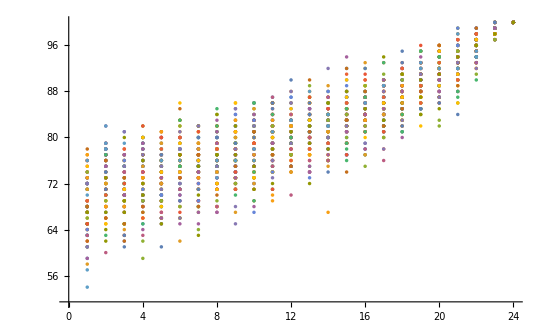

```mathematica
ListPlot[Inner[List, Range[1,24], #, List]& /@ reslists100]
```